```mathematica
{hmpgen1,hmpgen10,hmpgen50,hmpgen90,hmpgen99,hmpkeep1,hmpkeep10,hmpkeep50,hmpkeep90,hmpkeep99,hmpmem1,hmpmem10,hmpmem50,hmpmem90,hmpmem99,hmpkill1,hmpkill10,hmpkill50,hmpkill90,hmpkill99,hmptyp1,hmptyp10,hmptyp50,hmptyp90,hmptyp99}=Import["C:\\Users\\muxy1\\OneDrive\\桌面\\Modeling paper\\hmp500c24hpercent.mx"];
```

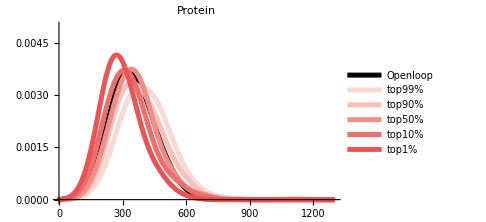

```mathematica
SmoothHistogram[{ol500c24h[[1]][[1]]/ol500c24h[[1]][[6]],hmpgen1[[1]][[1]]/hmpgen1[[1]][[6]],hmpgen10[[1]][[1]]/hmpgen10[[1]][[6]],hmpgen50[[1]][[1]]/hmpgen50[[1]][[6]],hmpgen90[[1]][[1]]/hmpgen90[[1]][[6]],hmpgen99[[1]][[1]]/hmpgen99[[1]][[6]]},50,PlotRange->{{0,1300},{0,0.005}},PlotLegends->{"Openloop","top99%","top90%","top50%","top10%","top1%"},PlotLabel->Style["Protein",Black,16],PlotStyle->{Directive[Black,Thickness[0.01]],Directive[RGBColor["#f8d9d3"],Thickness[0.01]],Directive[RGBColor["#f5c1ba"],Thickness[0.01]],Directive[RGBColor["#ef8d87"],Thickness[0.01]],Directive[RGBColor["#ed6f6d"],Thickness[0.01]],Directive[RGBColor["#eb5355"],Thickness[0.01]]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

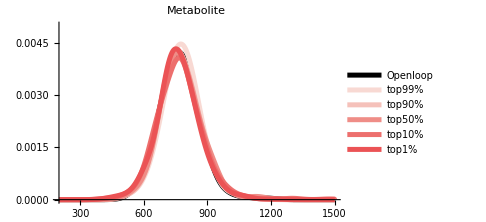

```mathematica
SmoothHistogram[{ol500c24h[[1]][[4]]/ol500c24h[[1]][[6]],hmpgen1[[1]][[4]]/hmpgen1[[1]][[6]],hmpgen10[[1]][[4]]/hmpgen10[[1]][[6]],hmpgen50[[1]][[4]]/hmpgen50[[1]][[6]],hmpgen90[[1]][[4]]/hmpgen90[[1]][[6]],hmpgen99[[1]][[4]]/hmpgen99[[1]][[6]]},40,PlotRange->{{200,1500},{0,0.005}},PlotLegends->{"Openloop","top99%","top90%","top50%","top10%","top1%"},PlotLabel->Style["Metabolite",Black,16],PlotStyle->{Directive[Black,Thickness[0.01]],Directive[RGBColor["#f8d9d3"],Thickness[0.01]],Directive[RGBColor["#f5c1ba"],Thickness[0.01]],Directive[RGBColor["#ef8d87"],Thickness[0.01]],Directive[RGBColor["#ed6f6d"],Thickness[0.01]],Directive[RGBColor["#eb5355"],Thickness[0.01]]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

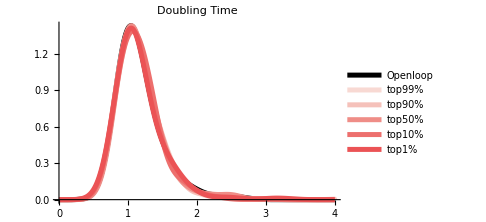

```mathematica
SmoothHistogram[{Log[2]/ol500c24h[[1]][[5]],Log[2]/hmpgen1[[1]][[5]],Log[2]/hmpgen10[[1]][[5]],Log[2]/hmpgen50[[1]][[5]],Log[2]/hmpgen90[[1]][[5]],Log[2]/hmpgen99[[1]][[5]]},0.15,PlotRange->{{0,4},Automatic},PlotLegends->{"Openloop","top99%","top90%","top50%","top10%","top1%"},PlotLabel->Style["Doubling Time",Black,16],PlotStyle->{Directive[Black,Thickness[0.01]],Directive[RGBColor["#f8d9d3"],Thickness[0.01]],Directive[RGBColor["#f5c1ba"],Thickness[0.01]],Directive[RGBColor["#ef8d87"],Thickness[0.01]],Directive[RGBColor["#ed6f6d"],Thickness[0.01]],Directive[RGBColor["#eb5355"],Thickness[0.01]]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

```mathematica
{hmpmem1,hmpmem10,hmpmem50,hmpmem90,hmpmem99}=Parallelize[{metabproteinmemfast[hmpkeep1],metabproteinmemfast[hmpkeep10],metabproteinmemfast[hmpkeep50],metabproteinmemfast[hmpkeep90],metabproteinmemfast[hmpkeep99]}];
```

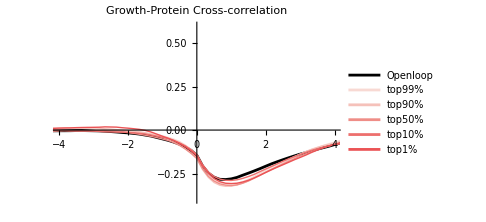

```mathematica
ListLinePlot[{ol500c24hmem[[4]],hmpmem1[[4]],hmpmem10[[4]],hmpmem50[[4]],hmpmem90[[4]],hmpmem99[[4]]},PlotRange->{{-4,4},{-0.4,0.6}},PlotLegends->{"Openloop","top99%","top90%","top50%","top10%","top1%"},PlotLabel->Style["Growth-Protein Cross-correlation",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#f8d9d3"],Thick],Directive[RGBColor["#f5c1ba"],Thick],Directive[RGBColor["#ef8d87"],Thick],Directive[RGBColor["#ed6f6d"],Thick],Directive[RGBColor["#eb5355"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

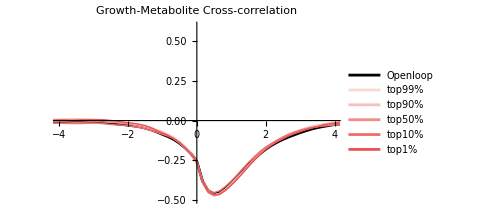

```mathematica
ListLinePlot[{ol500c24hmem[[5]],hmpmem1[[5]],hmpmem10[[5]],hmpmem50[[5]],hmpmem90[[5]],hmpmem99[[5]]},PlotRange->{{-4,4},{-0.5,0.6}},PlotLegends->{"Openloop","top99%","top90%","top50%","top10%","top1%"},PlotLabel->Style["Growth-Metabolite Cross-correlation",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#f8d9d3"],Thick],Directive[RGBColor["#f5c1ba"],Thick],Directive[RGBColor["#ef8d87"],Thick],Directive[RGBColor["#ed6f6d"],Thick],Directive[RGBColor["#eb5355"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

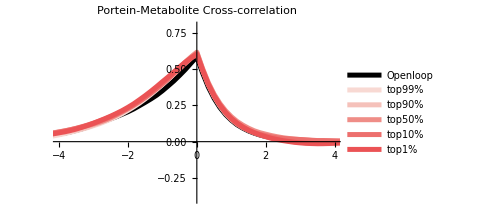

```mathematica
ListLinePlot[{ol500c24hmem[[6]],hmpmem1[[6]],hmpmem10[[6]],hmpmem50[[6]],hmpmem90[[6]],hmpmem99[[6]]},PlotRange->{{-4,4},{-0.4,0.8}},PlotLegends->{"Openloop","top99%","top90%","top50%","top10%","top1%"},PlotLabel->Style["Portein-Metabolite Cross-correlation",Black,16],PlotStyle->{Directive[Black,Thickness[0.01]],Directive[RGBColor["#f8d9d3"],Thickness[0.01]],Directive[RGBColor["#f5c1ba"],Thickness[0.01]],Directive[RGBColor["#ef8d87"],Thickness[0.01]],Directive[RGBColor["#ed6f6d"],Thickness[0.01]],Directive[RGBColor["#eb5355"],Thickness[0.01]]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

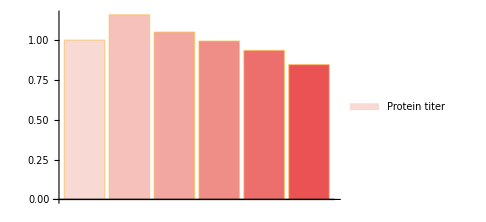

```mathematica
BarChart[{oltyp[[2]]/oltyp[[2]],hmptyp1[[2]]/oltyp[[2]],hmptyp10[[2]]/oltyp[[2]],hmptyp50[[2]]/oltyp[[2]],hmptyp90[[2]]/oltyp[[2]],hmptyp99[[2]]/oltyp[[2]]},ChartLegends->{"Protein titer"},ChartStyle->{RGBColor["#f8d9d3"],
RGBColor["#f5c1ba"],
RGBColor["#f2a8a1"],
RGBColor["#ef8d87"],
RGBColor["#ed6f6d"],
RGBColor["#eb5254"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

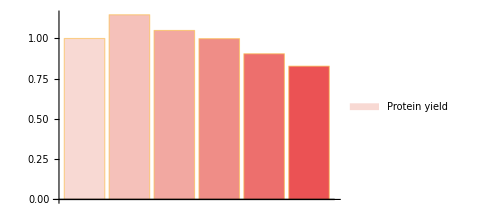

```mathematica
BarChart[{oltyp[[5]]/oltyp[[5]],hmptyp1[[5]]/oltyp[[5]],hmptyp10[[5]]/oltyp[[5]],hmptyp50[[5]]/oltyp[[5]],hmptyp90[[5]]/oltyp[[5]],hmptyp99[[5]]/oltyp[[5]]},ChartLegends->{"Protein yield"},ChartStyle->{RGBColor["#f8d9d3"],
RGBColor["#f5c1ba"],
RGBColor["#f2a8a1"],
RGBColor["#ef8d87"],
RGBColor["#ed6f6d"],
RGBColor["#eb5254"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

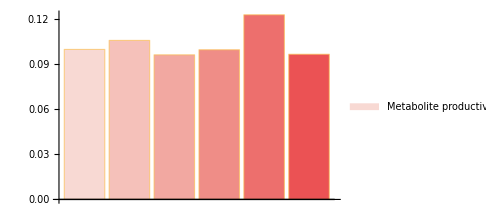

```mathematica
BarChart[{oltyp[[9]]/oltyp[[9]]-0.9,hmptyp1[[9]]/oltyp[[9]]-0.9,hmptyp10[[9]]/oltyp[[9]]-0.9,hmptyp50[[9]]/oltyp[[9]]-0.9,hmptyp90[[9]]/oltyp[[9]]-0.9,hmptyp99[[9]]/oltyp[[9]]-0.9},ChartLegends->{"Metabolite productivity"},ChartStyle->{RGBColor["#f8d9d3"],
RGBColor["#f5c1ba"],
RGBColor["#f2a8a1"],
RGBColor["#ef8d87"],
RGBColor["#ed6f6d"],
RGBColor["#eb5254"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

```mathematica
ListLinePlot[{oltyp[[1]],hmptyp1[[1]],hmptyp10[[1]],hmptyp50[[1]],hmptyp90[[1]],hmptyp99[[1]]},PlotLabel->"Protein titer",PlotStyle->{Black,
RGBColor["#f5c1ba"],
RGBColor["#f2a8a1"],
RGBColor["#ef8d87"],
RGBColor["#ed6f6d"],
RGBColor["#eb5254"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

-Graphics-

```mathematica
ListLinePlot[{oltyp[[3]],hmptyp1[[3]],hmptyp10[[3]],hmptyp50[[3]],hmptyp90[[3]],hmptyp99[[3]]},PlotLabel->"metabolite titer",PlotStyle->{Directive[Black,Thickness[0.01]],
Directive[RGBColor["#f5c1ba"],Thickness[0.01]],
Directive[RGBColor["#f2a8a1"],Thickness[0.01]],
Directive[RGBColor["#ef8d87"],Thickness[0.01]],Directive[RGBColor["#ed6f6d"],Thickness[0.01]],
Directive[RGBColor["#eb5254"],Thickness[0.01]]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

-Graphics-

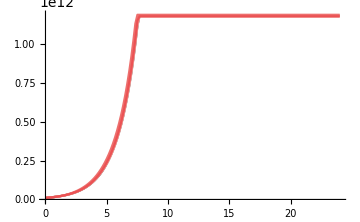

```mathematica
ListLinePlot[{Transpose@{ol500c24hkill[[All,1]],ol500c24hkill[[All,12]]},Transpose@{hmpkill1[[All,1]],hmpkill1[[All,12]]},Transpose@{hmpkill10[[All,1]],hmpkill10[[All,12]]},Transpose@{hmpkill50[[All,1]],hmpkill50[[All,12]]},Transpose@{hmpkill90[[All,1]],hmpkill90[[All,12]]},Transpose@{hmpkill99[[All,1]],hmpkill99[[All,12]]}},PlotStyle->{Black,
RGBColor["#f5c1ba"],
RGBColor["#f2a8a1"],
RGBColor["#ef8d87"],
RGBColor["#ed6f6d"],
RGBColor["#eb5254"]},AxesStyle->Directive[Black, 16],ImageSize->Medium, Axes->{True,True}]
```

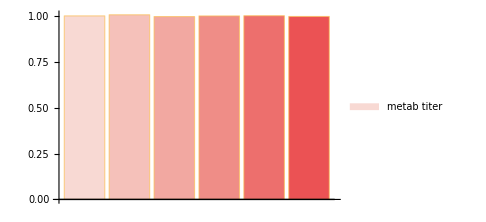

```mathematica
BarChart[{oltyp[[4]]/oltyp[[4]],hmptyp1[[4]]/oltyp[[4]],hmptyp10[[4]]/oltyp[[4]],hmptyp50[[4]]/oltyp[[4]],hmptyp90[[4]]/oltyp[[4]],hmptyp99[[4]]/oltyp[[4]]},ChartLegends->{"metab titer"},ChartStyle->{RGBColor["#f8d9d3"],
RGBColor["#f5c1ba"],
RGBColor["#f2a8a1"],
RGBColor["#ef8d87"],
RGBColor["#ed6f6d"],
RGBColor["#eb5254"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```